## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 20; mu = 0.2;
```

```mathematica
winit=(0.3-0.00005*I)
```

0.3-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.312484+1.47289×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

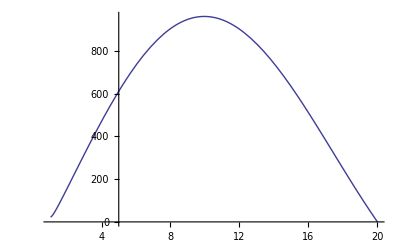

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.3+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.3+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{2.5,1.47314×10^-7},{2.475,1.37856×10^-7},{2.45,1.28814×10^-7},{2.425,1.20168×10^-7},{2.4,1.11914×10^-7},{2.375,1.04041×10^-7},{2.35,9.65421×10^-8},{2.325,8.94066×10^-8},{2.3,8.26295×10^-8},{2.275,7.61997×10^-8},{2.25,7.01096×10^-8},{2.225,6.4352×10^-8},{2.2,5.88693×10^-8},{2.175,5.3792×10^-8},{2.15,4.89743×10^-8},{2.125,4.44571×10^-8},{2.1,4.02207×10^-8},{2.075,3.62666×10^-8},{2.05,3.25827×10^-8},{2.025,2.91599×10^-8},{2.,2.59894×10^-8},{1.975,2.30625×10^-8},{1.95,2.03687×10^-8},{1.925,1.78998×10^-8},{1.9,1.56448×10^-8},{1.875,1.35986×10^-8},{1.85,1.17426×10^-8},{1.825,1.00776×10^-8},{1.8,8.57886×10^-9},{1.775,7.25251×10^-9},{1.75,6.06826×10^-9},{1.725,5.02705×10^-9},{1.7,4.11098×10^-9},{1.675,3.30548×10^-9},{1.65,2.59443×10^-9},{1.625,1.95021×10^-9},{1.6,1.35552×10^-9},{1.575,7.62947×10^-10},{1.55,1.76706×10^-10},{1.525,-4.88457×10^-10},{1.5,-1.27836×10^-9},{1.475,-2.25215×10^-9},{1.45,-3.50633×10^-9},{1.425,-5.11462×10^-9},{1.4,-7.26804×10^-9},{1.375,-1.01162×10^-8},{1.35,-1.35931×10^-8},{1.325,-1.81193×10^-8},{1.3,-2.38697×10^-8},{1.275,-3.10674×10^-8},{1.25,-3.99872×10^-8},{1.225,-5.09289×10^-8},{1.2,-6.42379×10^-8},{1.175,-8.02639×10^-8},{1.15,-9.94404×10^-8},{1.125,-1.222×10^-7},{1.1,-1.49033×10^-7},{1.075,-1.80473×10^-7},{1.05,-2.17097×10^-7},{1.025,-2.5953×10^-7},{1.,-3.08455×10^-7},{0.975,-3.64606×10^-7},{0.95,-4.28776×10^-7},{0.925,-5.01826×10^-7},{0.9,-5.84675×10^-7},{0.875,-6.78322×10^-7},{0.85,-7.83811×10^-7},{0.825,-9.0235×10^-7},{0.8,-1.03512×10^-6},{0.775,-1.18344×10^-6},{0.75,-1.3488×10^-6},{0.725,-1.53264×10^-6},{0.7,-1.73658×10^-6},{0.675,-1.96241×10^-6},{0.65,-2.21194×10^-6},{0.625,-2.48715×10^-6},{0.6,-2.79015×10^-6},{0.575,-3.12318×10^-6},{0.55,-3.48862×10^-6},{0.525,-3.88902×10^-6},{0.5,-4.32707×10^-6},{0.475,-4.80564×10^-6},{0.45,-5.32778×10^-6},{0.425,-5.89673×10^-6},{0.4,-6.51589×10^-6},{0.375,-7.18891×10^-6},{0.35,-7.91965×10^-6},{0.325,-8.71215×10^-6},{0.3,-9.57075×10^-6},{0.275,-0.0000105},{0.25,-0.0000115047},{0.225,-0.0000125899},{0.2,-0.0000137611},{0.175,-0.0000150238},{0.15,-0.0000163841},{0.125,-0.0000178482},{0.1,-0.0000194228},{0.075,-0.0000211149},{0.05,-0.0000229317},{0.025,-0.0000248811},{0.,-0.000026971}}

```mathematica
(*The imaginary part vs the radius*)
```

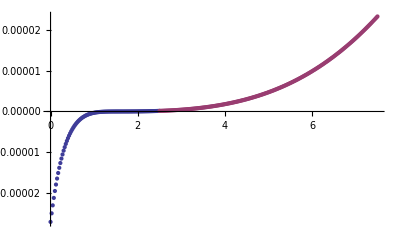

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

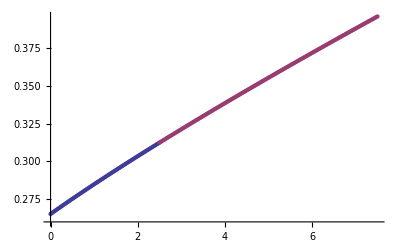

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=20/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=20/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=20/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=20/Q=0.999/I.dat